Joaquin Garcia Suarez (2026)

joaquin.garciasuarez@epfl.ch / ajgarciasuarez@gmail.com

```mathematica
currentDir=SetDirectory[NotebookDirectory[]]
```

/wolframcloud/userfiles/2ca/2ca429d5-762e-42e3-ad22-b259ece983bc/Millipede bar

```mathematica
SetDirectory[currentDir<>"/data"]
```

/wolframcloud/userfiles/2ca/2ca429d5-762e-42e3-ad22-b259ece983bc/Millipede bar/data

## Junction corner numbering

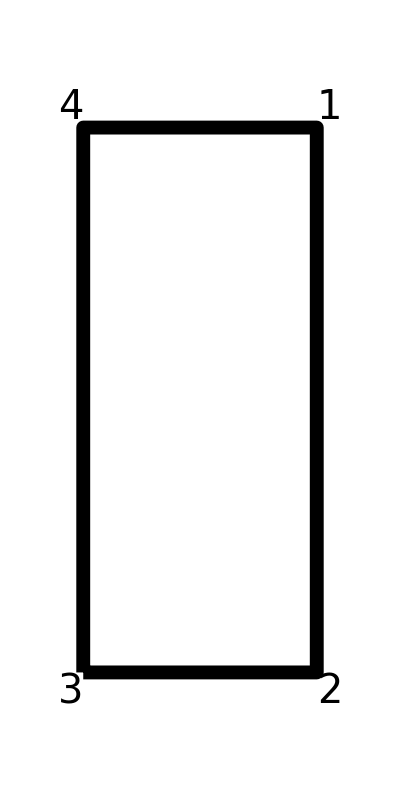

```mathematica
rectInset=Graphics[
{Thick,EdgeForm[{Black,Thickness[0.025]}],FaceForm[None],
(*Rectangle from {0,0} to {1,2}->width:height=1:2,vertical*)
Rectangle[{0,0},{1,2}],
(*Numbered corners:1–4 clockwise starting at top right*)
Text[Style["1",40],{1,2},{-1,-1}],(*top right*)
Text[Style["2",40],{1,0},{-1,1}],(*bottom right*)
Text[Style["3",40],{0,0},{1,1}],(*bottom left*)
Text[Style["4",40],{0,2},{1,-1}]   (*top left*)},
PlotRange->{{-0.2,1.2},{-0.2,2.2}},
AspectRatio->2  (*height/width=2->visually 1:2 vertical rectangle*),
Background->White]
```

## FEM data

```mathematica
data=Import["fe_corners.xlsx","Data"];
```

```mathematica
data=data[[1]];
```

Extract data

```mathematica
(*time*)
timeFEM=data[[;;,1]];
```

```mathematica
(*vertical movement of corners*)
yNode1=data[[;;,2]];
yNode2=data[[;;,3]];
yNode3=data[[;;,4]];
yNode4=data[[;;,5]];
```

```mathematica
(*horizontal movement of corners*)
xNode1=data[[;;,6]];
xNode2=data[[;;,7]];
xNode3=data[[;;,8]];
xNode4=data[[;;,9]];
```

#### Visualize

Timesteps are not uniform (?)

```mathematica
timesteps=(timeFEM[[2;;]]-timeFEM[[;;-2]]);
```

```mathematica
ListPlot[timesteps,Joined->True,AxesLabel->{"timestep","time increment [s]"}]
```

-Graphics-

Visualize displacements over time

Horizontal

```mathematica
ListPlot[{
Transpose@{timeFEM,xNode1*10^3},
Transpose@{timeFEM,xNode2*10^3},
Transpose@{timeFEM,xNode3*10^3},
Transpose@{timeFEM,xNode4*10^3}
},
GridLines->{{timeFEM[[400]](*arrival 2 junction*)},None},
AxesLabel->{"time [s]","horizontal displacement [mm]"},
PlotLegends->{"Node #1","Node #2","Node #3","Node #4"},
ImageSize->Large
]
```

-Graphics-

Vertical

```mathematica
ListPlot[{
Transpose@{timeFEM,yNode1*10^3},
Transpose@{timeFEM,yNode2*10^3},
Transpose@{timeFEM,yNode3*10^3},
Transpose@{timeFEM,yNode4*10^3}
},
GridLines->{{timeFEM[[400]](*arrival 2 junction*)},None},
AxesLabel->{"time [s]","vertical displacement [mm]"},
PlotLegends->{"Node #1","Node #2","Node #3","Node #4"},
ImageSize->Large
]
```

-Graphics-

## Important Parameters from experiments

#### DIC sampling

DIC software specifications

```mathematica
pixel2mm=1./12.;
```

Data sampling (mm)

```mathematica
xP1=1.3;
yP1=3.6;
```

#### Material properties

Steel Material Properties

```mathematica
density=7850.;
YoungMod=200.*10^9;
waveVel=Sqrt[YoungMod/density];(*m/s*)
```

System Geometry

```mathematica
L=5./1000; (*cross-section width [m] --  from older experiment*) 
Lprime=L/2.; (*because for the new transfer functions we use 2Lprime x 2Lprime for the cross-section dimensions*)
barLength=150./1000.; (*excluding junction*)
```

#### Pulse

```mathematica
pulseDur=55-20;(*μs, measured from plot -- see below*)
```

```mathematica
Tch=L/waveVel;
```

```mathematica
tStar=((pulseDur*10^-6)(*convert Tp to seconds before comparing*))/Tch
```

35.3328

Much greater than 1, we would expect good transmission  in the 1D cvase

```mathematica
Tchprime=L/2./waveVel; (*to reflect that in the second paper we use 4L' instead 2L to parametrize the total height of the junction*)
```

## Experiment 4 - Corners 1 & 2

#### General experiment settings

```mathematica
tshift=157.;
```

#### DIC horizontal displacement

```mathematica
dataRaw=Import["dic_corners_U.xlsx","Data"][[1]];
```

```mathematica
time=(First/@dataRaw);
uDispP1=(#[[2]]&/@dataRaw);
uDispP2=(Last/@dataRaw);
```

```mathematica
ListPlot[{
Transpose@{time-tshift,uDispP1*pixel2mm},
Transpose@{time-tshift,uDispP2*pixel2mm}
},Joined->True,
Axes->False,
Frame->True,
FrameStyle->Directive[Black,Thick,15],
FrameLabel->{"t [μs]","U [mm]"},
PlotRange->{{0,All},All},
PlotLegends->{"U P1","U P2"},
Background->White,
GridLines->All,
Epilog->{Black,
Line[{{25,-0.1},{25,0.15}}],
Line[{{25+2 barLength/waveVel*10^6,-0.1},{25+2 barLength/waveVel*10^6,0.15}}],
Text["Period between \n reflection \n from edge and back",Scaled[{0.275,.75}]]
}
]
```

-Graphics-

#### DIC vertical displacement

```mathematica
dataRaw=Import["dic_corners_V.xlsx","Data"][[1]];
```

```mathematica
time=(First/@dataRaw);
vDispP1=(#[[2]]&/@dataRaw);
vDispP2=(Last/@dataRaw);
```

```mathematica
ListPlot[{
Transpose@{time-tshift,vDispP1*pixel2mm},
Transpose@{time-tshift,vDispP2*pixel2mm}
},Joined->True,
Axes->False,
Frame->True,
FrameStyle->Directive[Black,Thick,15],
FrameLabel->{"t [μs]","V [mm]"},
PlotRange->{{0,All},All},
PlotLegends->{"V P1","V P2"},
Background->White,
GridLines->All,
Epilog->{Black,
Line[{{25,-0.1},{25,0.15}}],
Line[{{25+2 barLength/waveVel*10^6,-0.1},{25+2 barLength/waveVel*10^6,0.15}}],
Text["Period between \n reflection \n from edge and back",Scaled[{0.275,.275}]]
}
]
```

-Graphics-

#### Strain gauges

```mathematica
dataRaw=Import["gage_bars.xlsx","Data"][[1]];
```

```mathematica
time=(First/@dataRaw);
bar1Eps=(#[[2]]&/@dataRaw);
bar2Eps=(Last/@dataRaw);
```

```mathematica
ListPlot[{
Transpose@{time,bar1Eps},
Transpose@{time,bar2Eps}
},Joined->True,
Axes->False,
Frame->True,
FrameStyle->Directive[Black,Thick,15],
FrameLabel->{"t [μs]","ϵ [10^-6]"},
PlotRange->{{0,All},All},
PlotLegends->{"input bar","putput bar"},
Background->White,
GridLines->All]
```

-Graphics-

#### Prepare strain data for transfer functions:

Isolate the input

```mathematica
initialTpos=FirstPosition[time,_?(#>15&)][[1]];
endInputT=FirstPosition[time,_?(#>55&)][[1]];
finalTpos=FirstPosition[time,_?(#>85&)][[1]];
```

Convert experiment time in the range of the input to miliseconds

```mathematica
expTime=(time[[initialTpos;;finalTpos]]-time[[initialTpos]])*10^-6;(*seconds*)
inputList=bar1Eps[[initialTpos;;finalTpos]];
```

Save the input and output data, padded with zeros to remove reflections

```mathematica
inputList=Join[bar1Eps[[initialTpos;;endInputT]],ConstantArray[0.,finalTpos-endInputT]];
outputList=bar2Eps[[initialTpos;;finalTpos]];
```

Visualize

```mathematica
ListPlot[{
Transpose@{expTime/10^-6,outputList},
Transpose@{expTime/10^-6,inputList}
},Joined->True,
Axes->False,
Frame->True,
FrameStyle->Directive[Black,Thick,15],
FrameLabel->{"t [μs]","ϵ [μstrains]"},
PlotRange->{{0,expTime[[-1]]/10^-6},All},
PlotLegends->{"output bar","input bar"},
Background->White,
GridLines->All]
```

-Graphics-

Check that the stresses are consistent:

```mathematica
epsMax=Max@Abs[inputList];
sigmaMax=YoungMod*epsMax/10^6
```

4.73904×10^7

47 MPa, just like the other case!

#### Integrate input strain to obtain input displacement ϕ_i

Timestep

```mathematica
deltaTSG=Mean[expTime[[2;;]]-expTime[[;;-2]]];
```

Integrate input strain to get displacement input (ϕ_i) -> dx = waveVel*deltaTSG

```mathematica
dispInput=(waveVel*deltaTSG)*Table[
Total[inputList[[;;ii]]]*10^-3,(*mili strain -> get results in mm*)
{ii,1,Length@expTime}];
```

Interpolate to convolve later

```mathematica
auxData=Transpose@{expTime,dispInput};(*output units: mm | input units: s*)
inputDisp=Interpolation[auxData];(*output units: mm | input units: s*)
```

Visualize

```mathematica
Show[
Plot[inputDisp[t/10^6],{t,0,Max[expTime]*10^6},PlotStyle->Thickness[0.05],
Axes->False,
Frame->True,
FrameStyle->Directive[Black,Thick,15],
FrameLabel->{"t [μs]","U [mm]"},
PlotRange->{{0,All},All},
PlotLegends->{"Interpolation"},
Background->White,
GridLines->All
],
ListPlot[Transpose@{expTime*10^6,dispInput},Frame->False,PlotStyle->Red]
]
```

-Graphics-

## Comparison Experiments - Model : Strains (1D)

Heavy computations: recruit parallel kernels

```mathematica
CloseKernels[];
LaunchKernels[4];
```

#### Define inputs (either strains or displacements)

This is a bit redundant but I leave it as it is...

Strains (directly from strain gage)

```mathematica
auxData=Transpose@{expTime,inputList};(*output units: μ strain | input units: s*)
input=Interpolation[auxData];(*output units: μ strain | input units: s*)
```

Displacements (post-processed from integrating strains)

```mathematica
auxData=Transpose@{expTime,dispInput};(*output units: mm | input units: s*)
inputDisp=Interpolation[auxData];(*output units: mm | input units: s*)
```

#### Convolution integral to get output strain from input strain -- assuming 1D transmission

The 1D TF is much easier to handle, we can directly use the time-domain kernel instead of the transfer function, 
and we can do so w/ dimensions (unlike the 2D case that comes dimensionless and has to be carefully 
brought back to physical dimensions).

Everything here has units: both Tch and the the kernel (1/s), and the input (microstrains, i.e., 10**-6)

```mathematica
output[t_,T_]:=NIntegrate[-1.*Exp[-x/T]/T*input[t-x],{x,0,t}](*including -1 because of strain/stress sign flip not present in displacements*)
```

```mathematica
convol=ParallelTable[{expTime[[ii]],Quiet@output[expTime[[ii]],Tch]},{ii,1,Length@expTime}];
```

#### Plot

Both results are in microstrains

Set a delay patameter to align the experimental results with the predictions

```mathematica
delay=25.*10^-6;(*seconds*)
```

```mathematica
delayedConvol={(#[[1]]+delay)/10^-6,#[[2]]}&/@convol;
```

Visualize

```mathematica
ListPlot[{
Transpose@{expTime/10^-6,outputList},
delayedConvol
},
Joined->{False, True},
PlotStyle->{Black,Blue},
Frame->True,
FrameStyle->Directive[Black,Thick,15],
FrameLabel->{"t [μs]","ϵ[10^-6]"},
PlotLegends->Placed[{"data","prediction 1D"},Scaled[{0.8,0.75}]],
Background->White,
GridLines->All]
```

-Graphics-

From Andrés:

-Graphics-

Conclusion: the 1D transfer function overestimates the efficiency of the free junction!

## Align Data (DIC v. Strain Gauge)

#### Beware of different sampling rates:

Gauge data

```mathematica
dataRaw=Import["gage_bars.xlsx","Data"][[1]];
```

```mathematica
timeSG=(First/@dataRaw);
bar1Eps=(#[[2]]&/@dataRaw);
bar2Eps=(Last/@dataRaw);
```

time interval:

```mathematica
MinMax@timeSG
```

{-150.,349.9}

DIC data

```mathematica
dataRaw=Import["dic_corners_U.xls","Data"][[1]];
```

```mathematica
timeDIC=(First/@dataRaw);
uDispP1=(#[[2]]&/@dataRaw);
uDispP2=(Last/@dataRaw);
```

time interval:

```mathematica
MinMax@timeDIC
```

{0.,350.}

One has to align the time intervals carefully when making comparisons that mix 
strain gauge data and DIC displacement data

#### Comparing strain gage and DIC movements

```mathematica
size=600;
padding={{size/6.,size/8.},{size/8.,size/8.}};
```

```mathematica
p1=ListPlot[
(*Transpose@{expTime/10^-6,inputList},*)
Transpose@{timeSG,bar1Eps*YoungMod/10.^6},
PlotRange->{{0,193},Automatic},
PlotStyle->Blue,
Joined->True,
Frame->{{True,False},{True,False}},
FrameLabel->{"t [μs]",Style["ϵ[10^-6]",Blue]},
FrameStyle->Directive[Black,Thick,15,Blue],
PlotRange->{{0,expTime[[-1]]/10^-6},All},
(*PlotLegends->{"output bar"},*)
GridLines->All,
Background->White,
AspectRatio->1/2,
ImageSize->size,
ImagePadding->padding];
```

```mathematica
Max[timeDIC-tshift]
```

193.

Make sure that we add the pixel2mm factor to recover displacement in milimeters from DIC raw data (in pixels)

```mathematica
p2=ListPlot[
Transpose@{timeDIC-tshift,uDispP1*pixel2mm},
PlotRange->{{0,193},Automatic},
Joined->True,
PlotRange->{Automatic,Max[uDispP1*pixel2mm]*{-1,+1}},
PlotStyle->Red,
Frame->{{False,True},{False,True}},
FrameLabel->{{None,"U[mm]"},{None,None}},(*left axis belongs to p1*)
FrameStyle->Directive[Black,Thick,15,Red],
FrameTicks->All,
PlotRange->{{0,expTime[[-1]]/10^-6},All},
AspectRatio->1/2,
ImageSize->size,
ImagePadding->padding,
Background->None];
```

Show the two channels (gauge and DIC) overlapped:

```mathematica
Overlay[{p1,p2}]
```

-Graphics--Graphics-

The DIC data (red) is the integral of the strain data (blue).

#### Relevant time window (capture only the first pass)

```mathematica
size=600;
padding={{size/6.,size/8.},{size/8.,size/8.}};
```

```mathematica
p1=ListPlot[
Transpose@{expTime/10^-6,inputList},
PlotRange->{Automatic,Automatic},
PlotStyle->Blue,
Joined->True,
Frame->{{True,False},{True,False}},
FrameLabel->{"t [μs]",Style["ϵ[10^-6]",Blue]},
FrameStyle->Directive[Black,Thick,15,Blue],
PlotRange->{{0,expTime[[-1]]/10^-6},All},
(*PlotLegends->{"output bar"},*)
GridLines->All,
Background->White,
AspectRatio->1/2,
ImageSize->size,
ImagePadding->padding];
```

```mathematica
p2=ListPlot[
Transpose@{timeDIC-tshift,uDispP1*pixel2mm},
PlotRange->{{15.1,70+15.1},{-0.01,0.05}},
Joined->True,
PlotStyle->Red,
Frame->{{False,True},{False,True}},
FrameLabel->{{None,"U[mm]"},{None,None}},(*left axis belongs to p1*)
FrameStyle->Directive[Black,Thick,15,Red],
FrameTicks->All,
AspectRatio->1/2,
ImageSize->size,
ImagePadding->padding,
Background->None];
```

Show the two channels (gauge and DIC) overlapped:

```mathematica
Overlay[{p1,p2}]
```

-Graphics--Graphics-

The DIC data (red) is the integral of the strain data (blue).
This means that the experimental results are ready to compare with...

## Comparison Experiments - Model (horizontal displacements and rotations)

#### Get displacement of junction’s CoM

NOTE: here we do not use the analytical transfer function from the 2D model.
Why? because the TF is simple enough, and thus we avoid messing with the non-dimensionalization.
(in particular, we avoid the headache associated with the different characteristic length, 
i.e., we used cross section length =L in the 1D derivation, while 2L in the new 2D paper)

Now:
two options: integrate the input displacement (ϕ_i , obtained from integrating the strain) with the corresponding kernel or the strain directly with the corresponding kernel

```mathematica
outputU[t_,T_]:=NIntegrate[(1-Exp[-x/T])*input[t-x],{x,0,t}](*w/ units, strains come with μ factor, the integration time also already in seconds*)
```

```mathematica
outputDispU[t_,T_]:=NIntegrate[Exp[-x/T]/T*inputDisp[t-x],{x,0,t}](*w/ units, char. time in secs and displacement in milimeters, the integration time also already in seconds*)
```

Evaluate:

```mathematica
AbsoluteTiming[
convolU=ParallelTable[{expTime[[ii]],-1.*Quiet@outputU[expTime[[ii]],Tch]},{ii,1,Length@expTime}];
]
```

{79.6795,Null}

```mathematica
AbsoluteTiming[
convolDispU=ParallelTable[{expTime[[ii]],-1.*Quiet@outputDispU[expTime[[ii]],Tch]},{ii,1,Length@expTime}];
]
```

{71.4007,Null}

Save time [μs] - displacements [mm] pairs, ready for plotting

```mathematica
delayedConvol={(#[[1]]+delay/2)/10^-6,10^-3.*waveVel(#[[2]])}&/@convolU;(*gotta remove the mili factor, the wave velocity enters from converting the transfer function from disp-input to eps-input*)
delayedConvolDisp={(#[[1]]+delay/2)/10^-6,(#[[2]])}&/@convolDispU;
```

#### Sanity check (rule out issues with units/fudge factors)

Integrate also the displacement of the CoM from transfer function 
(recall all dimensionless TFs we use here are using Tch’ =c L’/2 = Tch/2)

```mathematica
junctionUcom[s_]=1/(1+2 s)
```

1/(1+2 s)

Get the analytical kernel from Laplace-inverting the TF at discrete  times

```mathematica
AbsoluteTiming[
uComKernelDisp=ParallelTable[
waveVel/Lprime*InverseLaplaceTransform[1/(1+2 s),s,N[expTime[[ii]]/Tchprime]],{ii,2,Length@expTime}];
]
```

{21.3771,Null}

Comparing the actual kernel and the numerical one

```mathematica
uComKernelDisp=Join[{uComKernelDisp[[1]]},uComKernelDisp];(*add one extra point to compensante the one lost during integration*)
```

```mathematica
test={#,Exp[-#/Tch]/Tch}&/@expTime;
```

```mathematica
Mean[(Last/@test)/uComKernelDisp]
```

1.00015

Visualize:

```mathematica
ListPlot[{
Transpose@{expTime,uComKernelDisp},
test
},Joined->{False, True}]
```

-Graphics-

Get the same displacement of CoM using the kernel directly from the dimensionless analytical 1D TF above

```mathematica
auxData=Transpose@{expTime,uComKernelDisp};
uComKernelDispTime=Interpolation[auxData];
```

```mathematica
outputDispUv2[t_]:=NIntegrate[uComKernelDispTime[x]*inputDisp[t-x],{x,0,t}]
```

```mathematica
AbsoluteTiming[
convolDispUv2=ParallelTable[{expTime[[ii]],-1.*Quiet@outputDispUv2[expTime[[ii]]]},{ii,1,Length@expTime}];
];
```

```mathematica
delayedConvolDispV2={(#[[1]]+delay/2)/10^-6,(#[[2]])}&/@convolDispUv2;(*gotta remove the mili factor, the wave velocity enters from converting the transfer function from disp-input to eps-input*)
```

#### Plot horizontal displacement of CoM (no rotation contribution)

```mathematica
p2=ListPlot[{
Transpose@{timeDIC-tshift,uDispP1*pixel2mm},
(**)
delayedConvolDisp,
delayedConvolDispV2
},
PlotRange->{{15.1,70+15.1},{-0.01,0.05}},
Joined->{True,True,False},
PlotStyle->{Red,{Black,Thickness[0.01]},Green},
Frame->{{False,True},{False,True}},
FrameLabel->{{None,"U[mm]"},{None,None}},(*left axis belongs to p1*)
FrameStyle->Directive[Black,Thick,15,Red],
FrameTicks->All,
AspectRatio->1/2,
ImageSize->size,
ImagePadding->padding,
Background->None,
PlotLegends->Placed[{"DIC Corner 1","CoM from convolution v1","CoM from convolution v2"}, Below]];
```

```mathematica
Overlay[{p1,p2}]
```

-Graphics--Graphics-

This image shows similar order of magnitude between CoM horizontal movement and the corner, but the corner’s being significantly higher due to rotation...

#### Get rotation

Dimensionless transfer function relating incoming displacement to CoM rotation:
Directly from the other Mathematica NB (solving system of equations in Laplace domain)

```mathematica
junctionRotLaplace[s_]=N@-(3 √2 3^(1/4) (1+√2 3^(1/4) √s) √s)/(√3+3 √2 3^(1/4) √s+2 √2 3^(3/4) √s+12 s+6 √3 s+16 √2 3^(1/4) s^(3/2)+20 √3 s^2)
```

-(5.58363 (1.+1.86121 √s) √s)/(1.73205+12.031 √s+22.3923 s+29.7794 s^(3/2)+34.641 s^2)

Get time-domain rotation kernel

Note: the TF above relates θ(s)=H_θ(s) ϕ_i(s), where s is the dimensionless Laplace variable.

Transfer function between rotation and displacement w/ dimensions back
1) Original one obtained from analysis (input is ϕ_i)
2) Need the change of variable from s_dimensionless to s (w/ units of frequency), s->c/(L/2)s_dimensionless
(L=2L’ is the cross-section of the square bar half side length, remember that the dimensionless freq. in the derivation is half)

```mathematica
AbsoluteTiming[
rotKernelDisp=ParallelTable[
waveVel/Lprime*InverseLaplaceTransform[junctionRotLaplace[s],s,N[expTime[[ii]]/Tchprime]],{ii,2,Length@expTime}];
]
```

{13.6145,Null}

Interpolate the discrete time kernel

```mathematica
rotKernelDisp=Join[{rotKernelDisp[[1]]},rotKernelDisp];
```

```mathematica
auxData=Transpose@{expTime,rotKernelDisp};
rotKernelDispTime=Interpolation[auxData];
```

Get rotation by convolving the interpolated kernel with the input displacement:

```mathematica
outputRotDisp[t_]:=NIntegrate[rotKernelDispTime[x]*inputDisp[t-x],{x,0,t}]
```

Evaluate the convolution numerically to get discrete values to predict experimental outcome:

```mathematica
AbsoluteTiming[
convolRotDisp=ParallelTable[{expTime[[ii]],1.*Quiet@outputRotDisp[expTime[[ii]]]},{ii,1,Length@expTime}];
]
```

{41.6162,Null}

```mathematica
ListPlot@convolRotDisp
```

-Graphics-

#### Plot rotation alone

Prepare prediction results with proper delay and units

```mathematica
delayedConvolRotOnlyDisp={(#[[1]]+1.delay/2)/10^-6,Lprime/L(#[[2]])}&/@convolRotDisp;
(*the conversion factor to go back to proper units*)
```

Visualize

```mathematica
p2=ListPlot[{
Transpose@{timeDIC-tshift,((uDispP1-uDispP2)*pixel2mm(*convert from pixel 2 mm*))/((2*yP1)(*use distance between the two points*))},
delayedConvolRotOnlyDisp
},
PlotRange->{{15.1,70+15.1},Automatic},
Joined->{False,False,False},
PlotStyle->{Red,Black,Green},
Frame->{{False,True},{False,True}},
FrameLabel->{{None,"θ[rad]"},{None,None}},(*left axis belongs to p1*)
FrameStyle->Directive[Black,Thick,15,Red],
FrameTicks->All,
AspectRatio->1/2,
ImageSize->size,
ImagePadding->padding,
Background->None];
Overlay[{p1,p2}]
```

-Graphics--Graphics-

## Paper’s plots

From here, this is just generating the panels in Fig.9 of the paper.

#### Rotations

```mathematica
Lfem=4./1000.;
```

FEM results to get rotation

```mathematica
thetaV1=(xNode2-xNode1)/(2Lfem);
thetaV2=(xNode3-xNode4)/(2Lfem);
thetaV3=(yNode3-yNode2)/Lfem;
thetaV4=(yNode4-yNode1)/Lfem;
```

```mathematica
femDelay=5;
```

```mathematica
ListPlot[{
Transpose@{timeFEM/10^-6,-thetaV1},
Transpose@{timeFEM/10^-6,-thetaV2},
Transpose@{timeFEM/10^-6,-thetaV3},
Transpose@{timeFEM/10^-6,-thetaV3}
},AxesLabel->{"t [μs]","θ[rad]"}]
```

-Graphics-

```mathematica
angleComp=ListPlot[{
Transpose@{timeDIC-tshift,(uDispP1-uDispP2)/(2yP1)*pixel2mm},
delayedConvolRotOnlyDisp,
Transpose@{timeFEM/10^-6+femDelay,-thetaV1}
},
PlotLabel->Style["CoM Rotation",20,Black],
Joined->{False,True,True},
PlotMarkers->{Automatic,None,None},
PlotStyle->{Black,
{Darker@Red,Thickness[0.01]},
{Black,Dashed,Thickness[0.01]}},
PlotRange->{{20,70},Automatic},
Axes->False,
Frame->True,
FrameStyle->Directive[Black,Thick,16],
FrameLabel->{"t [μs]","θ[rad]"},
PlotRange->{{0,expTime[[-1]]/10^-6},All},
PlotLegends->Placed[Style[#,20]&/@{"DIC","Model","FEM"},Scaled[{0.6,0.3}]],
Background->White,
GridLines->All,
ImageSize->400]
```

-Graphics-

```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/aj/Desktop/Work/Subhash

```mathematica
Export["angleComp_v2.pdf",angleComp]
```

angleComp_v2.pdf

#### Plot horizontal displacement including rotation contribution

```mathematica
delayedConvolRotDisp={#[[1]],yP1*(#[[2]])}&/@delayedConvolRotOnlyDisp;(*compute the contribnution to the displacement from rotation*)
```

```mathematica
totalDisp=Transpose@{delayedConvolRotDisp[[;;,1]],delayedConvolRotDisp[[;;,2]]+delayedConvolDisp[[;;,2]]};
```

Corner P1

```mathematica
uP1Comp=ListPlot[{
Transpose@{timeDIC-tshift,uDispP1*pixel2mm},
totalDisp,
Transpose@{timeFEM/10^-6+femDelay,xNode1/10^-3}
},
PlotLabel->Style["P1 Horizontal Displacement",20,Black],
Joined->{False,True,True},
PlotMarkers->{Automatic,None,None},
PlotStyle->{Black,
{Darker@Red,Thickness[0.01]},
{Black,Dashed,Thickness[0.01]}
},
PlotRange->{{20,70},{-0.01,0.06}},
Axes->False,
Frame->True,
FrameStyle->Directive[Black,Thick,16],
FrameLabel->{"t [μs]","U[mm]"},
PlotRange->{{0,expTime[[-1]]/10^-6},All},
PlotLegends->Placed[Style[#,20]&/@{"DIC","Model","FEM"},Scaled[{0.8,0.3}]],
(*
Epilog->Inset[
rectInset,(*the graphic we made above*)
Scaled[{0.2,0.6}],
{Right,Bottom},(*which corner of the inset is anchored there*)
Scaled[{0.3,0.60}] (*size:width,height;1:2 ratio kept->0.15:0.30*)],
*)
Background->White,
GridLines->All,
ImageSize->400]
```

-Graphics-

```mathematica
Export["uP1Comp_v2.pdf",uP1Comp]
```

uP1Comp_v2.pdf

Corner P2

```mathematica
totalDisp=Transpose@{delayedConvolRotDisp[[;;,1]],-1.0*delayedConvolRotDisp[[;;,2]]+delayedConvolDisp[[;;,2]]};
```

```mathematica
p2=ListPlot[{
Transpose@{timeDIC-tshift,uDispP2*pixel2mm},
delayedConvolDisp,
totalDisp},
PlotRange->{{15.1,70+15.1},{-0.01,0.05}},
Joined->{True,False,False},
PlotStyle->{Red,Black,Green},
Frame->{{False,True},{False,True}},
FrameLabel->{{None,"U[mm]"},{None,None}},(*left axis belongs to p1*)
FrameStyle->Directive[Black,Thick,15,Red],
FrameTicks->All,
AspectRatio->1/2,
ImageSize->size,
ImagePadding->padding,
Background->None];
```

```mathematica
uP2Comp=ListPlot[{
Transpose@{timeDIC-tshift,uDispP2*pixel2mm},
totalDisp,
Transpose@{timeFEM/10^-6+femDelay,xNode2/10^-3}
},
PlotLabel->Style["P2 Horizontal Displacement",20,Black],
Joined->{False,True,True},
PlotMarkers->{Automatic,None,None},
PlotStyle->{Black,
{Darker@Red,Thickness[0.01]},
{Black,Dashed,Thickness[0.01]}
},
PlotRange->{{20,70},{-0.011,0.03}},
Axes->False,
Frame->True,
FrameStyle->Directive[Black,Thick,16],
FrameLabel->{"t [μs]","U[mm]"},
PlotRange->{{0,expTime[[-1]]/10^-6},All},
PlotLegends->Placed[Style[#,20]&/@{"DIC","Model","FEM"},Scaled[{0.8,0.26}]],
Background->White,
GridLines->All,
ImageSize->400]
```

-Graphics-

```mathematica
Export["uP2Comp_v2.pdf",uP2Comp]
```

uP2Comp_v2.pdf

#### Vertical displacements

Transfer function (from the other NB)

```mathematica
junctionV[s_]=N[(3^(1/4) (√2 3^(3/4)+6 √s))/(√2 (√3+3 √2 3^(1/4) √s+2 √2 3^(3/4) √s+12 s+6 √3 s+16 √2 3^(1/4) s^(3/2)+20 √3 s^2))]
```

(0.930605 (3.22371+6. √s))/(1.73205+12.031 √s+22.3923 s+29.7794 s^(3/2)+34.641 s^2)

Evaluate the inverse  numerically, and bring it back to units:

```mathematica
AbsoluteTiming[
vKernelDisp=ParallelTable[
waveVel/Lprime*InverseLaplaceTransform[junctionV[s],s,N[expTime[[ii]]/Tchprime]],{ii,2,Length@expTime}];
]
```

{13.7383,Null}

Interpolate the kernel to compute the convolution later:

```mathematica
vKernelDisp=Join[{vKernelDisp[[1]]},vKernelDisp];
```

```mathematica
auxData=Transpose@{expTime,vKernelDisp};
vKernelDispTime=Interpolation[auxData];
```

Compute the convolution of the input displacement with the vertical displacement kernel for the junction CoM

```mathematica
outputVdispDisp[t_]:=NIntegrate[vKernelDispTime[x]*inputDisp[t-x],{x,0,t}]
```

```mathematica
AbsoluteTiming[
convolVdispDisp=ParallelTable[{expTime[[ii]],1.*Quiet@outputVdispDisp[expTime[[ii]]]},{ii,1,Length@expTime}];
]
```

{45.7309,Null}

Plot vertical displacement of CoM (no rotation contribution)

```mathematica
delayedConvolRotDispV={#[[1]],xP1*(#[[2]])}&/@delayedConvolRotOnlyDisp;
```

```mathematica
delayedConvolDispV={(#[[1]]+1.delay/2)/10^-6,-(#[[2]])}&/@convolVdispDisp;
```

```mathematica
totalDispV=Transpose@{delayedConvolRotDisp[[;;,1]],delayedConvolRotDispV[[;;,2]]+delayedConvolDispV[[;;,2]]};
```

```mathematica
vComp=ListPlot[{
Transpose@{timeDIC-tshift,vDispP2*pixel2mm},
Transpose@{timeDIC-tshift,vDispP1*pixel2mm},
totalDispV,
Transpose@{timeFEM/10^-6+femDelay,yNode2/10^-3},
Transpose@{timeFEM/10^-6+femDelay,yNode1/10^-3}
},
PlotLabel->Style["P2/P1 Vertical Displacement",20,Black],
Joined->{False,False,True,True,True},
PlotMarkers->{Automatic,Automatic,None,None,None},
PlotStyle->{Black,
Gray,
{Darker@Red,Thickness[0.01]},
{Gray,Dashed,Thickness[0.01]}
},
PlotRange->{{20,70},{-0.011,0.06}},
Axes->False,
Frame->True,
FrameStyle->Directive[Black,Thick,16],
FrameLabel->{"t [μs]","V[mm]"},
PlotRange->{{0,expTime[[-1]]/10^-6},All},
PlotLegends->Placed[Style[#,14]&/@{"DIC (P2)","DIC (P1)","Model","FEM (P2)","FEM (P1)"},Scaled[{0.80,0.275}]],
Background->White,
GridLines->All,
ImageSize->400]
```

-Graphics-

```mathematica
Export["vComp_v2.pdf",vComp]
```

vComp_v2.pdf